```mathematica
(*Computing the Discrepancy of a finite set of distinct points on S2 in the spirit of Niederreiter for star discrepancy. Algorithm described by me 9/22/2014*)

 (*NOT FULLY OPTIMIZED as of 9/24/2014 : Kusner *)

(*got rid of Cross[] and also added an IF statement for the case of antipodal points in the Dis2- cases, which was throwing a 1/0 indeterminate case.*)

(*Claim of general algorithm, O(C(d)n^d+k) for n points in SD, k universal and small, C linear in d and small
This should run faster with proper use of sorting and subsets, rather than mapping to the entire list, also MASSIVELY paralleizable*)

NMSQ[u_]:=u.u
NM[u_]:=Sqrt[u.u] 
NM::usage="NM[u] computes the vector norm of u.";

NTups[X_,n_]:=Subsets[X,{n}]
NTups::usage="NTups[X, n] generates all subsets with n elements of a finite set X";
```

```mathematica
(*Triples*)
CRS[u_,v_]:={u[[2]]v[[3]]-u[[3]]v[[2]], u[[3]]v[[1]]-u[[1]]v[[3]],u[[1]]v[[2]]-v[[1]]u[[2]]}
CRS::usage="CRS[u, v] computes the cross product of u and v";

VNMal[u_,v_,w_]:=CRS[u-w,v-w]/NM[CRS[u-w,v-w]]
VNMal::usage="VNMal[u, v, w] computes a unit normal vector to the plane defined by the points u, v and w.";

DiracCounter31[x_,u_,v_,w_]:=If[Dot[VNMal[u,v,w],u]<Dot[VNMal[u,v,w],x], 1,0]
DiracCounter31::usage="DiracCounter31[x, u, v, w] assigns a value of 1 to a point x if it falls within the OPEN cap defined by u, v and w and the choice of unit normal, 0 otherwise.";

DiracCounter32[x_,u_,v_,w_]:=If[Dot[VNMal[u,v,w],u]≤Dot[VNMal[u,v,w],x], 1,0]
DiracCounter32::usage="DiracCounter32[x, u, v, w] assigns a value of 1 to a point x if it falls within the CLOSED cap defined by u, v and w and the choice of unit normal, 0 otherwise.";

SigmaCounter31[u_,v_,w_] :=(1-Dot[VNMal[u,v,w],u])/2
SigmaCounter31::usage="SigmaCounter31[x, u, v, w] computes the normalized area of the cap defined by u, v and w and the choice of unit normal.";

LocalDis31[X_,u_,v_,w_]:=
Abs[NMSQ[Map[DiracCounter31[#,u,v,w]&,X]]/Length[X]-SigmaCounter31[u,v,w]]
LocalDis31::usage="LocalDis31[X, u, v, w] computes the discrepancy of a point set X with respect to the OPEN cap defined by u, v and w and the choice of unit normal.";

LocalDis32[X_,u_,v_,w_]:=
Abs[NMSQ[Map[DiracCounter32[#,u,v,w]&,X]]/Length[X]-SigmaCounter31[u,v,w]]
LocalDis32::usage="LocalDis32[X, u, v, w] computes the discrepancy of a point set X with respect to the CLOSED cap defined by u, v and w and the choice of unit normal.";

Dis31[X_]:=Map[LocalDis31[X,#[[1]],#[[2]],#[[3]]]&,NTups[X,3]]
Dis31::usage="Dis31[X] computes the discrepancy of a point set X with respect to all OPEN caps defined by triples of points in X and a choice of unit normal.";

Dis32[X_]:=Map[LocalDis32[X,#[[1]],#[[2]],#[[3]]]&,NTups[X,3]]
Dis32::usage="Dis32[X] computes the discrepancy of a point set X with respect to all CLOSED caps defined by triples of points in X and a choice of unit normal.";


Dis33[X_]:= {Max[Map[
Max[
LocalDis31[X,#[[1]],#[[2]],#[[3]]],
LocalDis32[X,#[[1]],#[[2]],#[[3]]]
]&,
NTups[X,3]
]]}


Dis33[{{1,0,0}, {0,1,0}, {0,0,1}}]
```

{1+1/2 (-1+1/(√3))}

```mathematica
(*Pairs*)
LNMal[u_,v_]:=(u+v)/NM[u+v]
VNMal::usage="VNMal[u, v] computes a unit normal vector to the plane defined by the points u, v when they are diametrically opposed in a cap.";

DiracCounter21[x_,u_,v_]:=If[NM[u+v]==0,0,If[Dot[LNMal[u,v],u]<Dot[LNMal[u,v],x], 1,0]]
DiracCounter21::usage="DiracCounter21[x, u, v] assigns a value of 1 to a point x if it falls within the OPEN cap defined by u and v being diametrically opposed and the choice of unit normal, 0 otherwise.";

DiracCounter22[x_,u_,v_]:=If[NM[u+v]==0,0,If[Dot[LNMal[u,v],u]<=Dot[LNMal[u,v],x], 1,0]]
DiracCounter22::usage="DiracCounter22[x, u, v] assigns a value of 1 to a point x if it falls within the CLOSED cap defined by u and v being diametrically opposed and the choice of unit normal, 0 otherwise.";

SigmaCounter21[u_,v_] :=If[NM[u+v]==0,0,(1-Dot[LNMal[u,v],u])/2]
SigmaCounter21::usage=
"SigmaCounter21[x, u, v] computes the normalized area of the cap defined by u and v being diametrically opposed and the choice of unit normal.";

LocalDis21[X_,u_,v_]:=
Abs[NMSQ[Map[DiracCounter21[#,u,v]&,X]]/Length[X]-SigmaCounter21[u,v]]
LocalDis21::usage="LocalDis21[X, u, v] computes the discrepancy of a point set X with respect to the OPEN cap defined by u and v being diametrically opposed and the choice of unit normal.";

LocalDis22[X_,u_,v_]:=
Abs[NMSQ[Map[DiracCounter22[#,u,v]&,X]]/Length[X]-SigmaCounter21[u,v]]
LocalDis22::usage="LocalDis22[X, u, v] computes the discrepancy of a point set X with respect to the CLOSED cap defined by u and v being diametrically opposed and the choice of unit normal.";

Dis21[X_]:=Map[LocalDis21[X,#[[1]],#[[2]]]&,NTups[X,2]]
Dis21::usage="Dis21[X] computes the discrepancy of a point set X with respect to all OPEN caps defined by diametrically opposed pairs of points in X and a choice of unit normal.";


Dis22[X_]:=Map[LocalDis22[X,#[[1]],#[[2]]]&,NTups[X,2]]
Dis22::usage="Dis21[X] computes the discrepancy of a point set X with respect to all CLOSED caps defined by diametrically opposed pairs of points in X and a choice of unit normal.";
```

```mathematica
S2InftyDisInit[X_]:=Max[Join[Dis22[X],Dis21[X],Dis31[X],Dis32[X],{1/Length[X]}]]
S2InftyDis[X_]:=Max[Join[Dis22[X],Dis21[X],Dis33[X],{1/Length[X]}]]
S2InftyDis::usage="SwInftyDis[X] computes the maximum discrepancy of the point set X with respect to the caps that are anchored by triples, pairs and singltons in X.  This equal to the S2 L-Infinity discrepancy of the set X.";
S2InftyDisN[X_]:=Max[Join[Dis22[N[X]],Dis21[N[X]],Dis31[N[X]],Dis32[N[X]],{1/Length[N[X]]}]]
```

```mathematica
FLPS[n_]:=Module[{Fn,r},Fn=Fibonacci[n];r=Fibonacci[n-1]/Fn;Table[{k/Fn,FractionalPart[k r]},{k,0,Fn-1}]];
```

```mathematica
Phi[x_,y_]:={2 √(y-y^2)Cos[2π x],2 √(y-y^2)Sin[2π x],1-2y};

sphFLPS[n_]:=Phi[#[[1]],#[[2]]]&/@FLPS[n];
spgFLPS::usage="generates Fobonacci points on the sphere. From Mathematica Notebook for Point Sets on the Sphere S2 with Smal Spherical Cap Discrepancy by Aisleitner, Brauchart and Dick."
```

generates Fobonacci points on the sphere. From Mathematica Notebook for Point Sets on the Sphere S2 with Smal Spherical Cap Discrepancy by Aisleitner, Brauchart and Dick.

```mathematica
S2InftyDisInit[N[sphFLPS[8]]]//Timing
```

{5.95373,0.168729}

```mathematica
S2InftyDis[N[sphFLPS[8]]]//Timing
```

{5.88976,0.168729}

```mathematica
S2InftyDis[N[sphFLPS[8]]]//Timing
```

{5.93743,0.168729}

```mathematica
S2InftyDis[N[sphFLPS[8]]]//Timing
```

{6.17416,0.168729}

```mathematica
z[th_]:=Sqrt[1-th^2]
TetPoints[th_]:= {
{0,th,z[th]},
{0,-th,z[th]},
{th,0,-z[th]},
{-th,0,-z[th]}
}
```

```mathematica
Dis33[TetPoints[.5]]
```

{0.379904}

```mathematica
NMinimize[{S2InftyDis[TetPoints[x]],x>0,x<1},x]
```

{0.375,{x→0.956016}}

```mathematica
NMinimize[{Dis33[TetPoints[x]][[1]],x>0,x<1},x]
```

{0.375,{x→0.956016}}

```mathematica
Graphics3D[{PointSize[Medium],Point@TetPoints[x],Opacity[.5], Sphere[{0,0,0}]}, Boxed->False]/.{x->0.9560163238272577}
```

-Graphics3D-

```mathematica
RootApproximant[Chop[x]]/.{x->0.9560163238272577}
```

Root[-2-3 #1+#1^2+2 #1^3-#1^6-#1^7-2 #1^8-#1^10+3 #1^11+3 #1^12+#1^13+3 #1^14&,2]

```mathematica
Minimize[{Dis31[TetPoints[x]][[1]],x>0,x<1},x]
Minimize[{Dis32[TetPoints[x]][[1]],x>0,x<1},x]
```

{1/3,{x→√(2/3)}}

{1/4,{x→0}}

```mathematica
Solve[Dis31[TetPoints[x]][[1]]==Dis32[TetPoints[x]][[1]]&&x>0&&x<1,x]
```

{{x→1/4 √(1/2 (19-√105))},{x→1/4 √(1/2 (19+√105))}}

```mathematica
Dis32[TetPoints[x]]/.{x->1/4 √(1/2 (19-√105))}//Simplify
```

{(512-√(210 (233+19 √105))+19 √(466+38 √105))/2048,(1024+√(210 (233+19 √105))-19 √(466+38 √105))/2048,(512-√(210 (233+19 √105))+19 √(466+38 √105))/2048,(1024+√(210 (233+19 √105))-19 √(466+38 √105))/2048}

```mathematica
{Dis31[TetPoints[x]][[1]],Dis32[TetPoints[x]][[1]]}/.{{x->-1},{x->1},{x->-1/4 √(1/2 (19-√105))},{x->1/4 √(1/2 (19-√105))},{x->-1/4 √(1/2 (19+√105))},{x->1/4 √(1/2 (19+√105))}}//N
```

{{0.5,0.5},{0.5,0.5},{0.375,0.375},{0.375,0.375},{0.375,0.375},{0.375,0.375}}

```mathematica
Graphics3D[{PointSize[Medium],Point@TetPoints[x],Opacity[.5], Sphere[{0,0,0}]}, Boxed->False]/.{{x->-1},{x->1},{x->-1/4 √(1/2 (19-√105))},{x->1/4 √(1/2 (19-√105))},{x->-1/4 √(1/2 (19+√105))},{x->1/4 √(1/2 (19+√105))}}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
TetPoints[x]/.{x->1/4 √(1/2 (19+√105))}
```

{{0,1/4 √(1/2 (19+√105)),√(1+1/32 (-19-√105))},{0,-1/4 √(1/2 (19+√105)),√(1+1/32 (-19-√105))},{1/4 √(1/2 (19+√105)),0,-√(1+1/32 (-19-√105))},{-1/4 √(1/2 (19+√105)),0,-√(1+1/32 (-19-√105))}}

```mathematica
TetPoints[x]/.{x->1/4 √(1/2 (19-√105))}
```

{{0,1/4 √(1/2 (19-√105)),√(1+1/32 (-19+√105))},{0,-1/4 √(1/2 (19-√105)),√(1+1/32 (-19+√105))},{1/4 √(1/2 (19-√105)),0,-√(1+1/32 (-19+√105))},{-1/4 √(1/2 (19-√105)),0,-√(1+1/32 (-19+√105))}}

```mathematica
Graphics3D[{PointSize[Medium],Point@TetPoints[x],Opacity[.5], Sphere[{0,0,0}]}, Boxed->False]/.{x->Sqrt[2/3]}
```

```mathematica
TetPoints[x]/.{x->Sqrt[2/3]}
```

{{0,√(2/3),1/(√3)},{0,-√(2/3),1/(√3)},{√(2/3),0,-1/(√3)},{-√(2/3),0,-1/(√3)}}

```mathematica
TetraPts={{1,0,-1/Sqrt[2]},{-1,0,-1/Sqrt[2]}, {0,1,1/Sqrt[2]},{0,-1,1/Sqrt[2]}}/NM[{1,0,-1/Sqrt[2]}]
```

{{√(2/3),0,-1/(√3)},{-√(2/3),0,-1/(√3)},{0,√(2/3),1/(√3)},{0,-√(2/3),1/(√3)}}

```mathematica
TetPoints[0]
```

{{0,0,1},{0,0,1},{0,0,-1},{0,0,-1}}

```mathematica
TetPoints[1]
```

{{0,1,0},{0,-1,0},{1,0,0},{-1,0,0}}

```mathematica
Graphics3D[{PointSize[Medium],Point@TetPoints[x],Opacity[.5], Sphere[{0,0,0}]}, Boxed->False]/.{x->1}
```

-Graphics3D-

```mathematica
Graphics3D[{PointSize[Medium],Point@TetPoints[x],Opacity[.5], Sphere[{0,0,0}]}, Boxed->False]/.{x->0}
```

-Graphics3D-

```mathematica
{{0,1/4 √(1/2 (19+√105)),√(1+1/32 (-19-√105))},{0,-1/4 √(1/2 (19+√105)),√(1+1/32 (-19-√105))},{1/4 √(1/2 (19+√105)),0,-√(1+1/32 (-19-√105))},{-1/4 √(1/2 (19+√105)),0,-√(1+1/32 (-19-√105))}}
```

```mathematica
{ArcSin[x],ArcCos[x]}/.{{x->1/4 √(1/2 (19+√105))},{x->√(1+1/32 (-19-√105))}}//N
```

{{1.27311,0.297691},{0.297691,1.27311}}

```mathematica
{ArcSin[x],ArcCos[x]}/.{{x->√(2/3)},{x->1/(√3)}}//N
```

{{0.955317,0.61548},{0.61548,0.955317}}

```mathematica
Dot[{0,1/4 √(1/2 (19+√105)),√(1+1/32 (-19-√105))}-{0,-1/4 √(1/2 (19+√105)),√(1+1/32 (-19-√105))},{1/4 √(1/2 (19+√105)),0,-√(1+1/32 (-19-√105))}-{-1/4 √(1/2 (19+√105)),0,-√(1+1/32 (-19-√105))}]
```

0

```mathematica
T=Dot[{0,1/4 √(1/2 (19+√105)),√(1+1/32 (-19-√105))}-{0,-1/4 √(1/2 (19+√105)),-√(1+1/32 (-19-√105))},{1/4 √(1/2 (19+√105)),0,-√(1+1/32 (-19-√105))}-{-1/4 √(1/2 (19+√105)),0,√(1+1/32 (-19-√105))}]
```

-4 (1+1/32 (-19-√105))

```mathematica
ArcCos[T]
```

```mathematica
ArcCos[-4 (1+1/32 (-19-√105))]//N
```

```mathematica
180-1.9221095891752316/(2Pi)*360
```

69.8712

```mathematica
{x}/.{{x->-1},{x->1},{x->-1/4 √(1/2 (19-√105))},{x->1/4 √(1/2 (19-√105))},{x->-1/4 √(1/2 (19+√105))},{x->1/4 √(1/2 (19+√105))}}//N
```

{{-1.},{1.},{-0.523004},{0.523004},{-0.956016},{0.956016}}

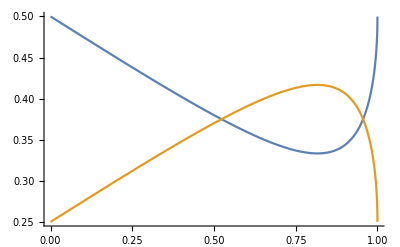

```mathematica
Plot[{Dis31[TetPoints[x]][[1]],Dis32[TetPoints[x]][[1]]},{x,0,1}]
```

```mathematica
Dis31[]
```

{}

```mathematica
Dis31[TetraPts]
```

{1/3,5/12,1/3,5/12}

```mathematica
1/2-5/12 == 1/3-1/4
```

True

```mathematica
SigmaCounter31[{0,1/4 √(1/2 (19-√105)),√(1+1/32 (-19+√105))},{0,-1/4 √(1/2 (19-√105)),√(1+1/32 (-19+√105))},{1/4 √(1/2 (19-√105)),0,-√(1+1/32 (-19+√105))}]//N
```

0.375